## Exercise Session 2, November 14

### Problem 1.1 b)

```mathematica
(* a simple example of a plot similar to that required in Problem 1.1 b) *)
f = x^3+b+c*x^2;
```

```mathematica
ContourPlot3D[f==0,{x,-1,1},{b,-1,1},{c,-1,1},AxesLabel->{"x","b","c"}]
```

-Graphics3D-

### Problem 1.2 a)

{x→-b}

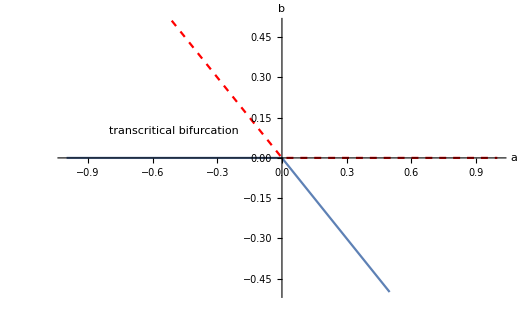

```mathematica
(* this is a simple example of how to generate a plot similar to that required in Problem 1.2a) *)
(* define the flow *)
g= x(x+b);
(* put the fixed points into sol *)
sol = Solve[g==0,x][[2]]
(* split solutions into stable and unstable parts*)
plot1=Plot[UnitStep[-D[g,x]]*x/.sol,{b,-1,1},PlotRange->{Automatic,{-0.5,0.5}}] (*stable*);
plot2=Plot[UnitStep[D[g,x]]*x/.sol,{b,-1,1},PlotStyle->{Red,Dashed}](*unstable*);
(* make text to add to the plot*)
text1 = Graphics[Text[Style["transcritical bifurcation",Large],{-0.5,0.1}]];
(* unify all the plots into one *)
Show[plot1,plot2,text1,AxesLabel->{"a","b"}]
(*Plot[HeavisideTheta[D[f,x]]**)
```